# MixedEulerianGraphQ

Yields True if the strongly connected mixed graph g is Eulerian or unicursal, and False otherwise

## Definition

```mathematica
ClearAll[MixedEulerianGraphQ]
MixedEulerianGraphQ[graph_?(ConnectedGraphQ[#]∧MixedGraphQ[#]&)]:=AllTrue[Subsets[VertexList[graph]],EdgeCount[graph,Alternatives@@#->_]-EdgeCount[graph,_->Alternatives@@#]<=EdgeCount[graph,_<->Alternatives@@#]&](*balanced set condition*)∧AllTrue[VertexDegree[graph],EvenQ](*even condition*)
```

## Documentation

### Usage

MixedEulerianGraphQ[g]

Yields Truepaclet:ref/True if the strongly connected mixed graph g is Eulerian or unicursal, and Falsepaclet:ref/False otherwise.

### Details & Options

Eulerian graphs have applications in arc routing and operations research.

EulerianGraphQ works for undirected graphs, directed graphs, and multigraphs but not mixed graphs. This function meets that need.

A mixed graph that is strongly connected is Eulerian, or unicursal, if and only if the graph is even (meaning all nodes/vertices are connected to an even number of other nodes/vertices and have an even degree) and the graph satisfied the balanced set condition, which states that for any subset of vertices/nodes, the difference between the number of arcs entering and the number of arcs leaving is less than or equal to the number of edges incident with the vertices/nodes.

## Examples

### Basic Examples

Test if a mixed graph is Eulerian:

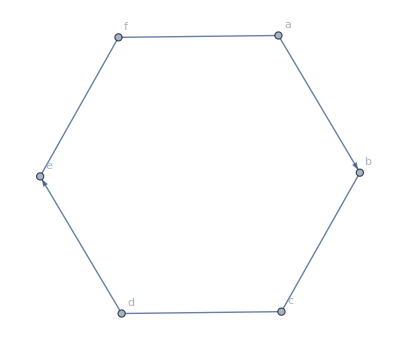

```mathematica
Graph[{a,b,c,d,e,f},{a->b,b<->c,c<->d,d->e,e<->f,a<->f},VertexLabels->Automatic,ImageSize->Automatic]
```

```mathematica
MixedEulerianGraphQ[Graph[{a,b,c,d,e,f},{a->b,b<->c,c<->d,d->e,e<->f,a<->f},VertexLabels->Automatic,ImageSize->Automatic]]
```

True

Although this graph is even, the graph violates the balanced set condition and is therefore not Eulerian:

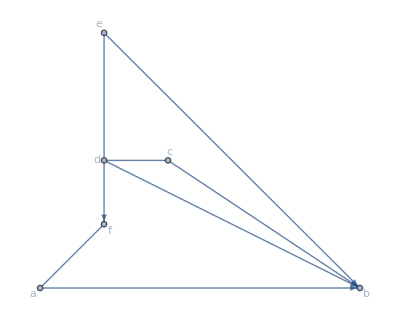

```mathematica
Graph[{a->b,b<->c,c<->d,d->b,d<->e,d->f,f<->a,e->b},VertexLabels->Automatic,GraphLayout->"PlanarEmbedding"]
```

```mathematica
MixedEulerianGraphQ[Graph[{a->b,b<->c,c<->d,d->b,d<->e,d->f,f<->a,e->b},VertexLabels->Automatic,GraphLayout->"PlanarEmbedding"]]
```

False

### Possible Issues

A graph that is beyond a limit of around 14 nodes can take an unreasonable amount of time because the number n of subsets grows exponentially according to O(2^n):

```mathematica
MixedEulerianGraphQ[Graph[{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v},{a->b,b<->c,c<->d,d->b,d<->e,d->f,f<->a,e->b,g<->e,h<->g,i<->g,j<->e,k<->j,l<->k,m<->l,n<->m,m<->o,o<->p,p<->q,q<->r,r<->s,s<->t,t<->u,u<->v},VertexLabels->Automatic]]//AbsoluteTiming
```

{218.966,False}

## Source & Additional Information

### Contributed By

Peter Cullen Burbery

### Keywords

Graph Theory

Networks

Flows in networks

Mathematical optimization

Eulerian graphs

Mixed graphs

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

EulerianGraphQ

MixedGraphQ

### Related Resource Objects

EulerizeGraph

UndirectedGraphToMixedGraph

RandomMixedGraph

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

13.1+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.